### Fidelity and probability expressions

```mathematica
ClearAll["Global`*"];
FDistillASAP = (-6 ⅇ^((2 T)/c+3 T λ) (-1+c λ) (2+c λ) (3+2 c (-1+F0) λ)-2 c ⅇ^(3 T λ) (-1+4 F0) λ (-1+c λ) (-19+16 F0+10 c (-1+F0) λ)+ⅇ^(2 T (1/c+2 λ)) (-2+c λ) (-1+c λ) (9+c (5-4 F0+8 F0^2) λ)+c ⅇ^(4 T λ) (-1+4 F0) λ (2+c λ) (1+c λ+8 F0 (-2+c λ))+ⅇ^(2 T (1/c+λ)) (2+c λ) (-27+c λ (25+4 c λ+8 F0 (8-F0+5 c (-2+F0) λ))))/(4 (-1+c λ) (-c^2 ⅇ^(3 T λ) (1-4 F0)^2 λ^2+ⅇ^(2 T (1/c+λ)) (2+c λ) (27+c (-13-4 F0+8 F0^2) λ)+ⅇ^(2 T (1/c+2 λ)) (-2+c λ) (9+c (5-4 F0+8 F0^2) λ)+9 ⅇ^((2 T)/c+3 T λ) (-4+c^2 λ^2)));
PDistillASAP = 1/(9 (-4+c^2 λ^2))ⅇ^(-2 T (1/c+2 λ)) (-c^2 ⅇ^(3 T λ) (1-4 F0)^2 λ^2+ⅇ^(2 T (1/c+λ)) (2+c λ) (27+c (-13-4 F0+8 F0^2) λ)+ⅇ^(2 T (1/c+2 λ)) (-2+c λ) (9+c (5-4 F0+8 F0^2) λ)+9 ⅇ^((2 T)/c+3 T λ) (-4+c^2 λ^2));
FDistillALAP = (5 c^2 (1-4 F0)^2 λ^2 ⅇ^(-(4 T)/c)+6 c (4 F0-1) λ (c λ-2) ⅇ^(-(2 T)/c)-20 c (4 F0-1) λ (2 c (F0-1) λ+3) ⅇ^(-T (2/c+λ))-12 (c λ-2) ⅇ^(λ (-T)) (2 c (F0-1) λ+3)+ⅇ^(-2 λ T) (8 c λ (10 F0 (c (F0-2) λ+3)+c λ+6)-108)+9 (c λ-2)^2)/(4 (c λ-2)^2 ((c^2 (1-4 F0)^2 λ^2 ⅇ^(-(4 T)/c))/(c λ-2)^2-(2 c^2 (1-4 F0)^2 λ^2 ⅇ^(-T (2/c+λ)))/(c λ-2)^2+(2 ⅇ^(-2 λ T) (c λ (c (8 F0^2-4 F0-13) λ+54)-54))/(c λ-2)^2+18 ⅇ^(λ (-T))+9));
PDistillALAP = 1/18 ((c^2 (1-4 F0)^2 λ^2 ⅇ^(-(4 T)/c))/(c λ-2)^2-(2 c^2 (1-4 F0)^2 λ^2 ⅇ^(-T (2/c+λ)))/(c λ-2)^2+(2 ⅇ^(-2 λ T) (c λ (c (8 F0^2-4 F0-13) λ+54)-54))/(c λ-2)^2+18 ⅇ^(λ (-T))+9);
(*FDiscard = (1-Exp[-2 λ T])^(-1)*(1/4-(1/4) Exp[-2 λ T]+2 λ (F0-1/4)*((Exp[-λ T]+1) (Exp[-2 T/c]-Exp[-λ T])/(λ-2/c)-(Exp[-2 T/c]-Exp[-2 λ T])/(2 λ-2/c)));*)
FDiscard = 1/(8 (-2+c λ))(-2+c λ+2 c ⅇ^(-T λ) (1-4 F0) λ+2 c ⅇ^(-T (2/c+λ)) (-1+4 F0) λ+(c^2 ⅇ^(-(2 T)/c) (-1+4 F0) λ^2)/(-1+c λ)+(ⅇ^(-2 T λ) (-2+c λ (3-4 c F0 λ)))/(-1+c λ)) (1+Coth[T λ]);
PDiscard = 1-E^(-2λ T);
xlogx[F_]:=If[F==0,0,F Log2[F]];
CohInfo[F_]:=Max[1+xlogx[F]+xlogx[1-F]-(1-F)Log2[3],0];
```

### Font size setting

```mathematica
FntSize = 24;
```

### Case 1

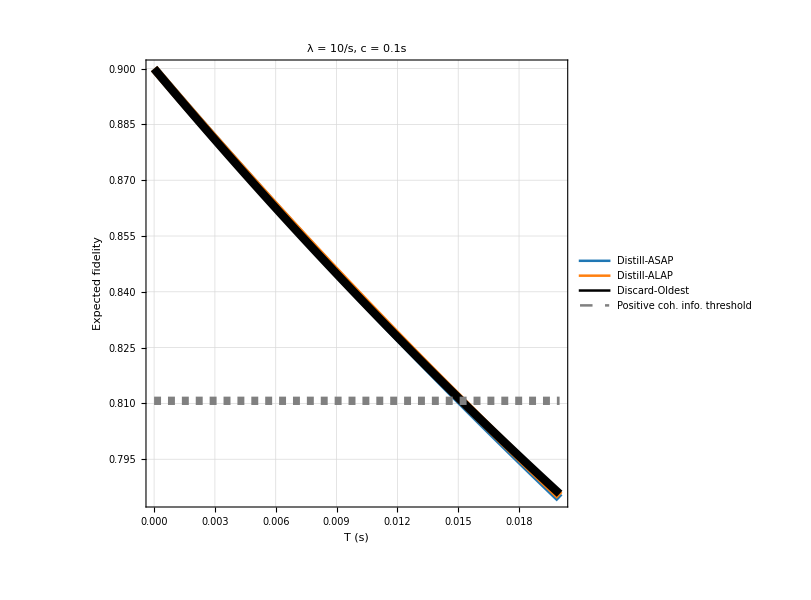

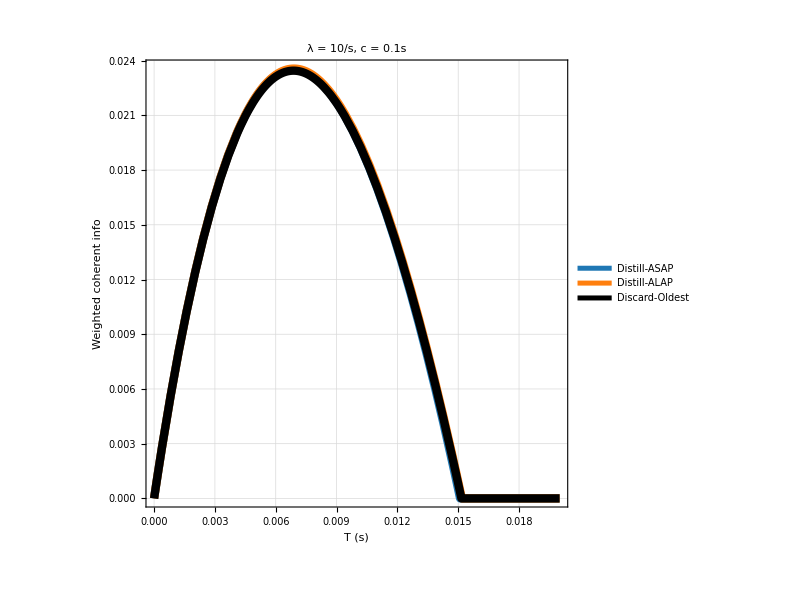

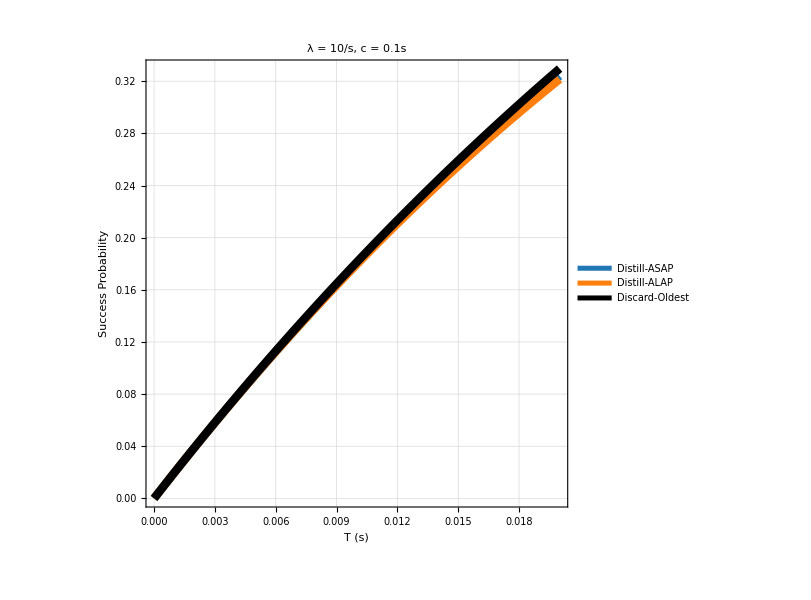

```mathematica
Substitution1 = {λ->10,c->0.1,F0->0.9};
FDistillASAPLimit = Limit[FDistillASAP, Substitution1];
FDistillALAPLimit = Limit[FDistillALAP,Substitution1];
FimitDiscardLimit = Limit[FDiscard,Substitution1];
Plot1 = Plot[
{FDistillASAPLimit,
FDistillALAPLimit,
FimitDiscardLimit,
0.8107},
{T,0,0.2c/.Substitution1},
PlotStyle->Map[Directive[Thickness[0.01],#]&,{RGBColor["#1f77b4"],RGBColor["#ff7f0e"],Black,Directive[Dashed,Gray]}],
PlotLabel->Style[StringForm["λ = ``/s, c = ``s", λ/.Substitution1,c/.Substitution1], Bold, Black],
PlotLegends->Placed[LineLegend[{"Distill-ASAP","Distill-ALAP","Discard-Oldest","Positive coh. info. threshold"},LegendFunction->(Framed[#,Background->White,FrameStyle->GrayLevel[0.8]]&)],{Right,Top}],
AspectRatio->1,
FrameLabel->{"T (s)","Expected fidelity"}, 
GridLines->Automatic, 
LabelStyle->{FontSize-> 18}, 
Frame->True,
ImageSize->600]
Plot7 = Plot[
{(PDistillASAP/.Substitution1 )*CohInfo[FDistillASAPLimit],
(PDistillALAP/.Substitution1 )*CohInfo[FDistillALAPLimit],
(PDiscard/.Substitution1) *CohInfo[FimitDiscardLimit]},
{T,0,0.2c/.Substitution1},
PlotStyle->Map[Directive[Thickness[0.01],#]&,{RGBColor["#1f77b4"],RGBColor["#ff7f0e"],Black,Directive[Dashed,Gray]}],
PlotLabel->Style[StringForm["λ = ``/s, c = ``s", λ/.Substitution1,c/.Substitution1], Bold, Black],
PlotLegends->Placed[LineLegend[{"Distill-ASAP","Distill-ALAP","Discard-Oldest","Positive coh. info. threshold"},LegendFunction->(Framed[#,Background->White,FrameStyle->GrayLevel[0.8]]&)],{Right,Top}],
AspectRatio->1,
FrameLabel->{"T (s)","Weighted coherent info"}, 
GridLines->Automatic, 
LabelStyle->{FontSize-> FntSize}, 
Frame->True,
ImageSize->600]
Plot13 = Plot[
{(PDistillASAP/.Substitution1 ),
(PDistillALAP/.Substitution1 ),
(PDiscard/.Substitution1)},
{T,0,0.2c/.Substitution1},
PlotStyle->Map[Directive[Thickness[0.01],#]&,{RGBColor["#1f77b4"],RGBColor["#ff7f0e"],Black,Directive[Dashed,Gray]}],
PlotLabel->Style[StringForm["λ = ``/s, c = ``s", λ/.Substitution1,c/.Substitution1], Bold, Black],
PlotLegends->Placed[LineLegend[{"Distill-ASAP","Distill-ALAP","Discard-Oldest","Positive coh. info. threshold"},LegendFunction->(Framed[#,Background->White,FrameStyle->GrayLevel[0.8]]&)],{Left,Top}],
AspectRatio->1,
FrameLabel->{"T (s)","Success Probability"}, 
GridLines->Automatic, 
LabelStyle->{FontSize-> FntSize}, 
Frame->True,
ImageSize->600]
```

### Case 2

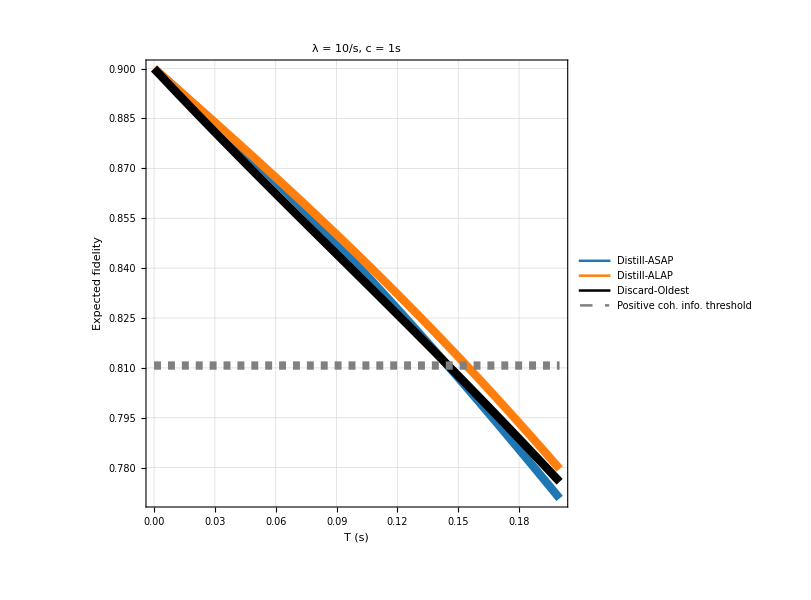

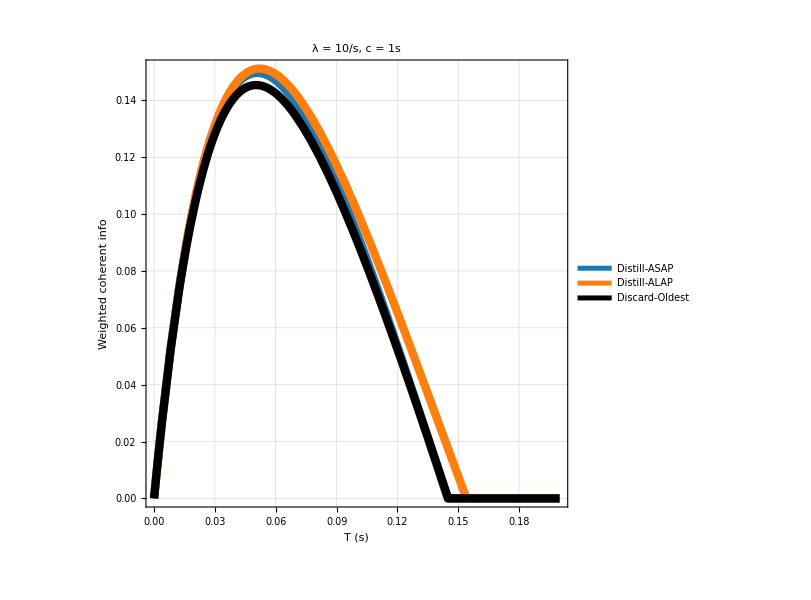

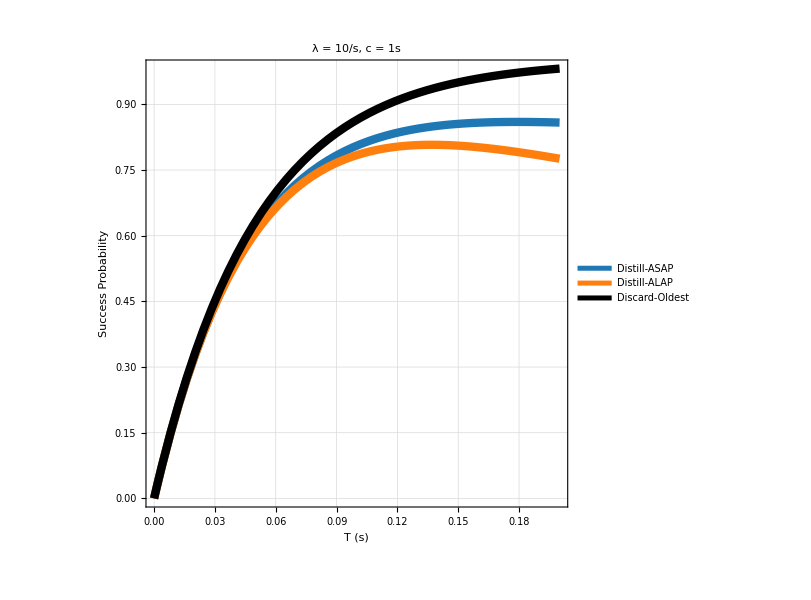

```mathematica
Substitution2 = {λ->10,c->1,F0->0.9};
Plot2 = Plot[
{FDistillASAP/.Substitution2,
FDistillALAP/.Substitution2,
FDiscard/.Substitution2,
0.8107},
{T,0,0.2c /. Substitution2},
PlotStyle->Map[Directive[Thickness[0.01],#]&,{RGBColor["#1f77b4"],RGBColor["#ff7f0e"],Black,Directive[Dashed,Gray]}],
PlotLabel->Style[StringForm["λ = ``/s, c = ``s", λ/.Substitution2,c/.Substitution2], Bold, Black],
PlotLegends->Placed[LineLegend[{"Distill-ASAP","Distill-ALAP","Discard-Oldest","Positive coh. info. threshold"},LegendFunction->(Framed[#,Background->White,FrameStyle->GrayLevel[0.8]]&)],{Right,Top}],
AspectRatio->1,
FrameLabel->{"T (s)","Expected fidelity"}, 
GridLines->Automatic, 
LabelStyle->{FontSize-> FntSize}, 
Frame->True,
ImageSize->600]

Plot8 = Plot[
{(PDistillASAP/.Substitution2 )*CohInfo[FDistillASAP/.Substitution2],
(PDistillALAP/.Substitution2 )*CohInfo[FDistillALAP/.Substitution2],
(PDiscard/.Substitution2) *CohInfo[FDiscard/.Substitution2]},
{T,0,0.2c/.Substitution2},
PlotStyle->Map[Directive[Thickness[0.01],#]&,{RGBColor["#1f77b4"],RGBColor["#ff7f0e"],Black,Directive[Dashed,Gray]}],
PlotLabel->Style[StringForm["λ = ``/s, c = ``s", λ/.Substitution2,c/.Substitution2], Bold, Black],
PlotLegends->Placed[LineLegend[{"Distill-ASAP","Distill-ALAP","Discard-Oldest","Positive coh. info. threshold"},LegendFunction->(Framed[#,Background->White,FrameStyle->GrayLevel[0.8]]&)],{Right,Top}],
AspectRatio->1,
FrameLabel->{"T (s)","Weighted coherent info"}, 
GridLines->Automatic, 
LabelStyle->{FontSize-> FntSize}, 
Frame->True,
ImageSize->600]

Plot14 = Plot[
{(PDistillASAP/.Substitution2 ),
(PDistillALAP/.Substitution2 ),
(PDiscard/.Substitution2)},
{T,0,0.2c/.Substitution2},
PlotStyle->Map[Directive[Thickness[0.01],#]&,{RGBColor["#1f77b4"],RGBColor["#ff7f0e"],Black,Directive[Dashed,Gray]}],
PlotLabel->Style[StringForm["λ = ``/s, c = ``s", λ/.Substitution2,c/.Substitution2], Bold, Black],
PlotLegends->Placed[LineLegend[{"Distill-ASAP","Distill-ALAP","Discard-Oldest","Positive coh. info. threshold"},LegendFunction->(Framed[#,Background->White,FrameStyle->GrayLevel[0.8]]&)],{Left,Top}],
AspectRatio->1,
FrameLabel->{"T (s)","Success Probability"}, 
GridLines->Automatic, 
LabelStyle->{FontSize-> FntSize}, 
Frame->True,
ImageSize->600]
```

### Case 3

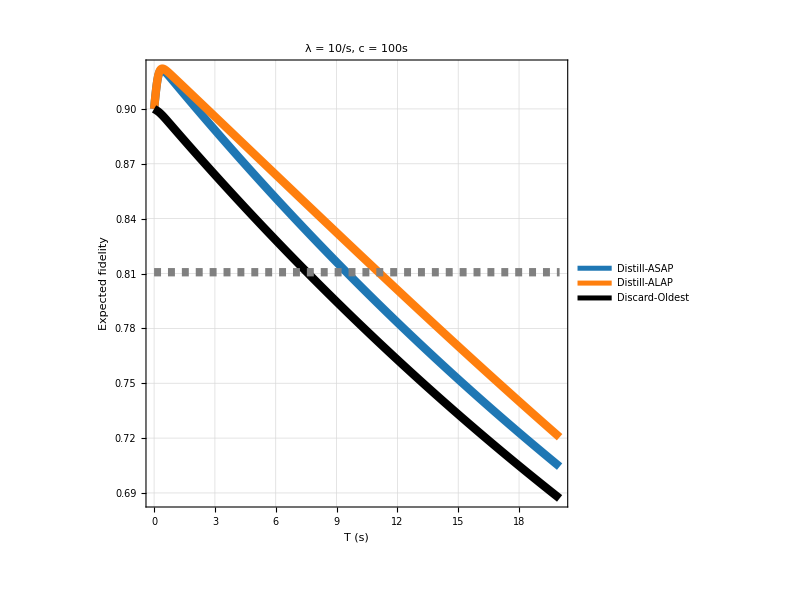

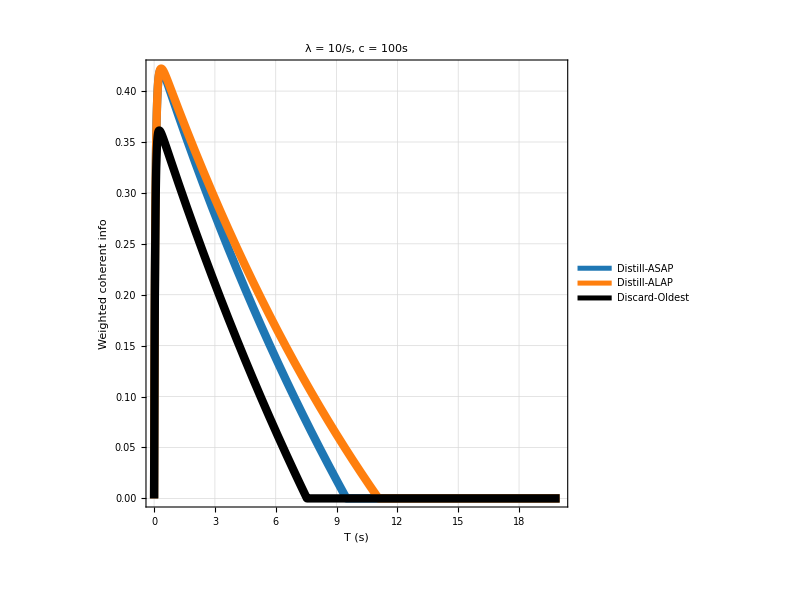

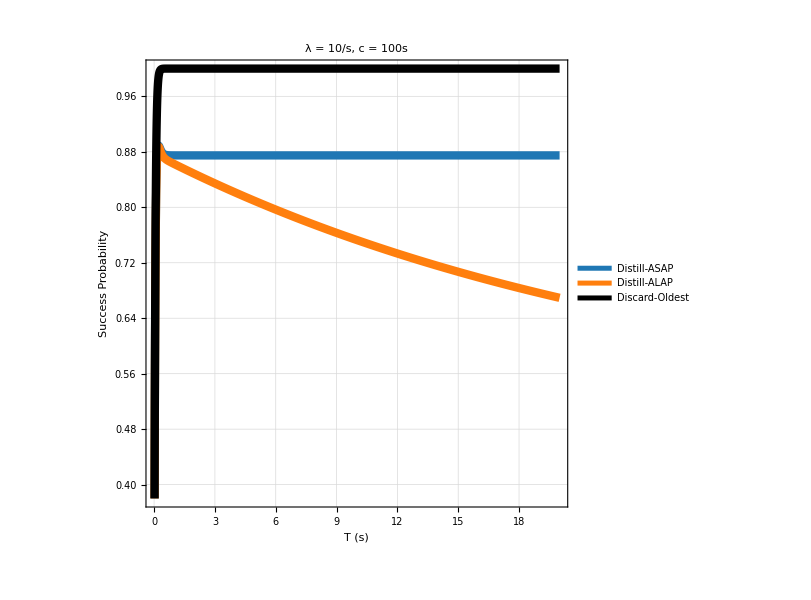

```mathematica
Substitution3 = {λ->10,c->100,F0->0.9};
Plot3 = Plot[
{FDistillASAP/.Substitution3,
FDistillALAP/.Substitution3,
FDiscard/.Substitution3,
0.8107},
{T,0,0.2c /. Substitution3},
PlotStyle->Map[Directive[Thickness[0.01],#]&,{RGBColor["#1f77b4"],RGBColor["#ff7f0e"],Black,Directive[Dashed,Gray]}],
PlotLabel->Style[StringForm["λ = ``/s, c = ``s", λ/.Substitution3,c/.Substitution3], Bold, Black],
PlotLegends->Placed[LineLegend[{"Distill-ASAP","Distill-ALAP","Discard-Oldest"},LegendFunction->(Framed[#,Background->White,FrameStyle->GrayLevel[0.8]]&)],{Right,Top}],
AspectRatio->1,
FrameLabel->{"T (s)","Expected fidelity"}, 
GridLines->Automatic, 
LabelStyle->{FontSize-> FntSize}, 
Frame->True,
ImageSize->600]
Plot9 = Plot[
{(PDistillASAP/.Substitution3 )*CohInfo[FDistillASAP/.Substitution3],
(PDistillALAP/.Substitution3 )*CohInfo[FDistillALAP/.Substitution3],
(PDiscard/.Substitution3) *CohInfo[FDiscard/.Substitution3]},
{T,0,0.2c/.Substitution3},
PlotStyle->Map[Directive[Thickness[0.01],#]&,{RGBColor["#1f77b4"],RGBColor["#ff7f0e"],Black,Directive[Dashed,Gray]}],
PlotLabel->Style[StringForm["λ = ``/s, c = ``s", λ/.Substitution3,c/.Substitution3], Bold, Black],
PlotLegends->Placed[LineLegend[{"Distill-ASAP","Distill-ALAP","Discard-Oldest","Positive coh. info. threshold"},LegendFunction->(Framed[#,Background->White,FrameStyle->GrayLevel[0.8]]&)],{Right,Top}],
AspectRatio->1,
FrameLabel->{"T (s)","Weighted coherent info"}, 
GridLines->Automatic, 
LabelStyle->{FontSize-> FntSize}, 
Frame->True,
ImageSize->600]

PDistillASAPSimplified3=Simplify[PDistillASAP/.Substitution3];
Plot15 = Plot[
{PDistillASAPSimplified3,
PDistillALAP/.Substitution3 ,
PDiscard/.Substitution3},
{T,0,0.2c/.Substitution3},
PlotStyle->Map[Directive[Thickness[0.01],#]&,{RGBColor["#1f77b4"],RGBColor["#ff7f0e"],Black,Directive[Dashed,Gray]}],
PlotLabel->Style[StringForm["λ = ``/s, c = ``s", λ/.Substitution3,c/.Substitution3], Bold, Black],
PlotLegends->Placed[LineLegend[{"Distill-ASAP","Distill-ALAP","Discard-Oldest","Positive coh. info. threshold"},LegendFunction->(Framed[#,Background->White,FrameStyle->GrayLevel[0.8]]&)],{Left,Bottom}],
AspectRatio->1,
FrameLabel->{"T (s)","Success Probability"}, 
GridLines->Automatic, 
LabelStyle->{FontSize-> FntSize}, 
Frame->True,
ImageSize->600]
```

### Case 4

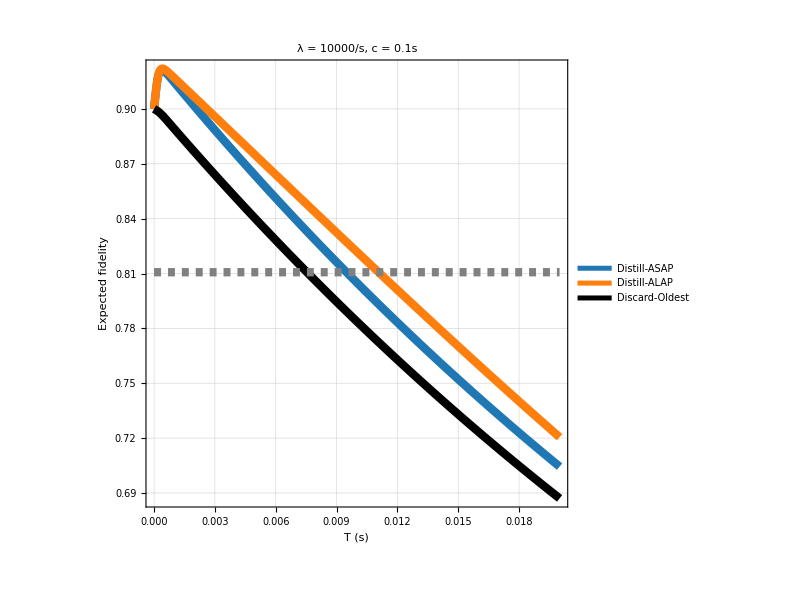

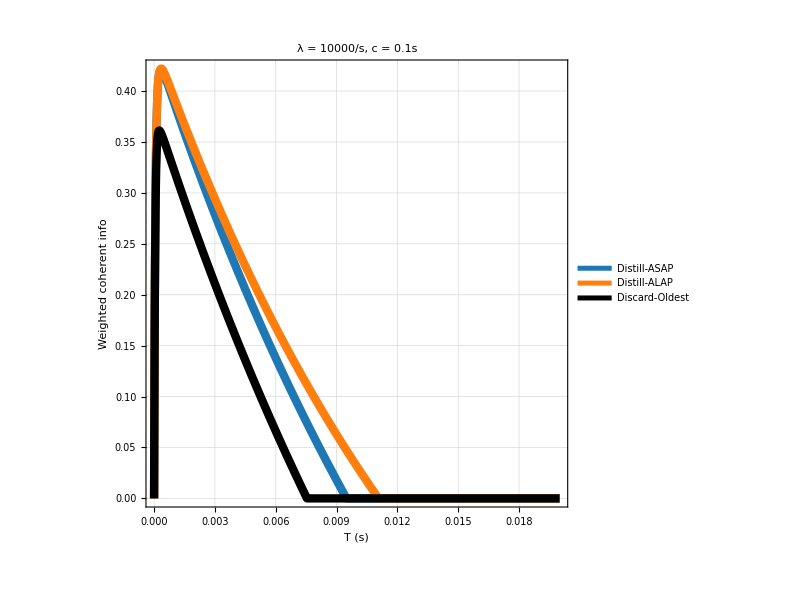

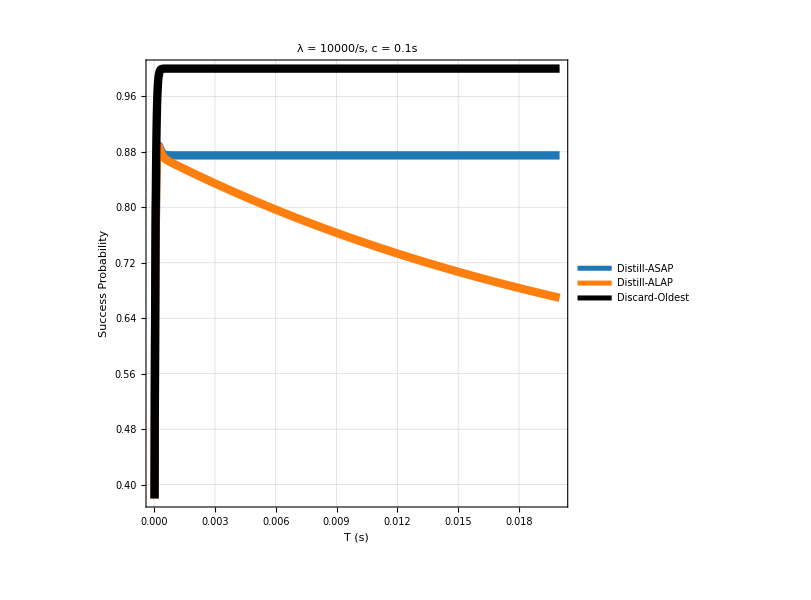

```mathematica
Substitution4 = {λ->10000,c->0.1,F0->0.9};
Plot4 = Plot[
{FDistillASAP/.Substitution4,
FDistillALAP/.Substitution4,
FDiscard/.Substitution4,0.8107},
{T,0,0.2c /. Substitution4},
PlotStyle->Map[Directive[Thickness[0.01],#]&,{RGBColor["#1f77b4"],RGBColor["#ff7f0e"],Black,Directive[Dashed,Gray]}],
PlotLabel->Style[StringForm["λ = ``/s, c = ``s", λ/.Substitution4,c/.Substitution4], Bold, Black],
PlotLegends->Placed[LineLegend[{"Distill-ASAP","Distill-ALAP","Discard-Oldest"},LegendFunction->(Framed[#,Background->White,FrameStyle->GrayLevel[0.8]]&)],{Right,Top}],
AspectRatio->1,
FrameLabel->{"T (s)","Expected fidelity"}, 
GridLines->Automatic, 
LabelStyle->{FontSize-> FntSize}, 
Frame->True,
ImageSize->600]

Plot10 = Plot[
{(PDistillASAP/.Substitution4 )*CohInfo[FDistillASAP/.Substitution4],
(PDistillALAP/.Substitution4 )*CohInfo[FDistillALAP/.Substitution4],
(PDiscard/.Substitution4) *CohInfo[FDiscard/.Substitution4]},
{T,0,0.2c/.Substitution4},
PlotStyle->Map[Directive[Thickness[0.01],#]&,{RGBColor["#1f77b4"],RGBColor["#ff7f0e"],Black,Directive[Dashed,Gray]}],
PlotLabel->Style[StringForm["λ = ``/s, c = ``s", λ/.Substitution4,c/.Substitution4], Bold, Black],
PlotLegends->Placed[LineLegend[{"Distill-ASAP","Distill-ALAP","Discard-Oldest","Positive coh. info. threshold"},LegendFunction->(Framed[#,Background->White,FrameStyle->GrayLevel[0.8]]&)],{Right,Top}],
AspectRatio->1,
FrameLabel->{"T (s)","Weighted coherent info"}, 
GridLines->Automatic, 
LabelStyle->{FontSize-> FntSize}, 
Frame->True,
ImageSize->600]

PDistillASAPSimplified4=Simplify[PDistillASAP/.Substitution4];
Plot16 = Plot[
{PDistillASAPSimplified4,
(PDistillALAP/.Substitution4 ),
(PDiscard/.Substitution4)},
{T,0,0.2c/.Substitution4},
PlotStyle->Map[Directive[Thickness[0.01],#]&,{RGBColor["#1f77b4"],RGBColor["#ff7f0e"],Black,Directive[Dashed,Gray]}],
PlotLabel->Style[StringForm["λ = ``/s, c = ``s", λ/.Substitution4,c/.Substitution4], Bold, Black],
PlotLegends->Placed[LineLegend[{"Distill-ASAP","Distill-ALAP","Discard-Oldest","Positive coh. info. threshold"},LegendFunction->(Framed[#,Background->White,FrameStyle->GrayLevel[0.8]]&)],{Left,Bottom}],
AspectRatio->1,
FrameLabel->{"T (s)","Success Probability"}, 
GridLines->Automatic, 
LabelStyle->{FontSize-> FntSize}, 
Frame->True,
ImageSize->600]
```

### Case 5

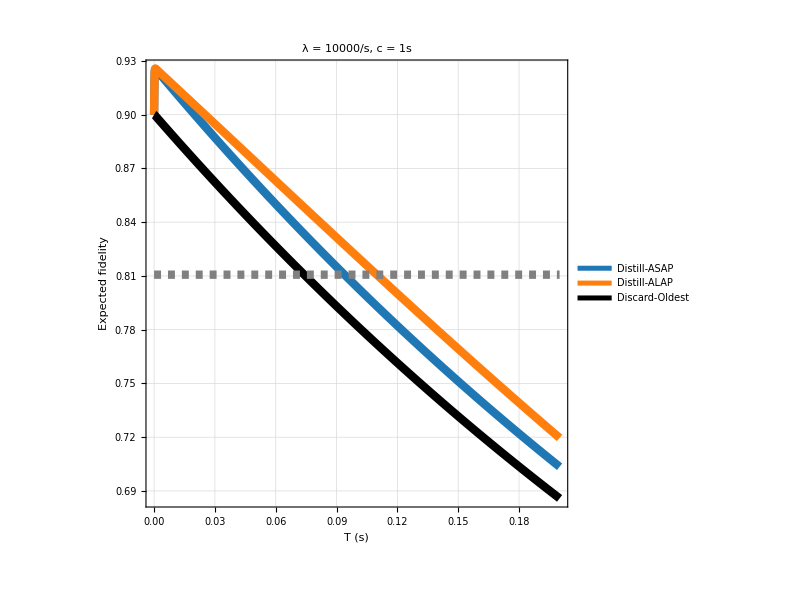

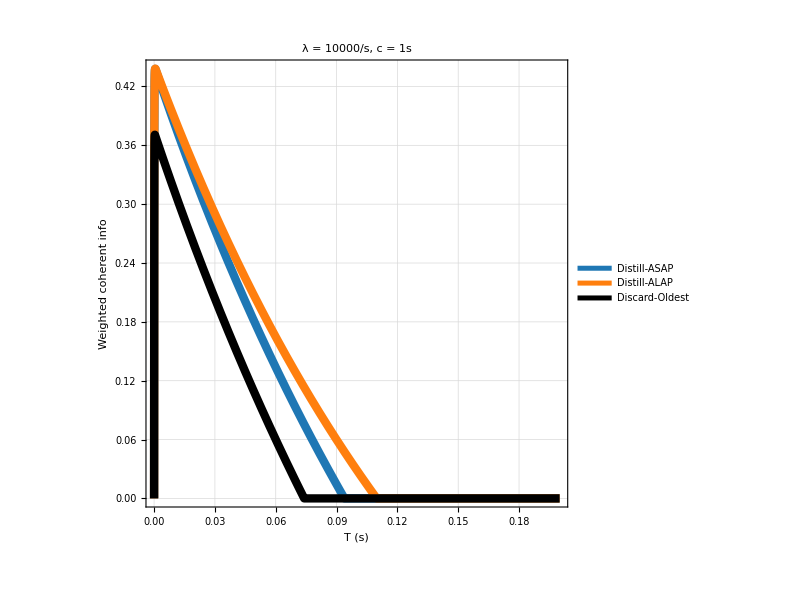

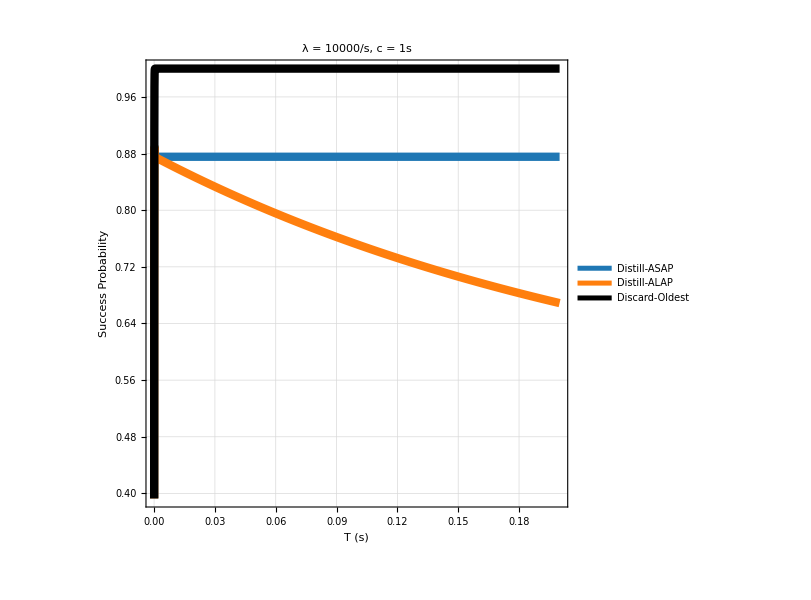

```mathematica
Substitution5= {λ->10000,c->1,F0->0.9};
Plot5 = Plot[
{FDistillASAP/.Substitution5,
FDistillALAP/.Substitution5,
FDiscard/.Substitution5,
0.8107},
{T,0,0.2c /. Substitution5},
PlotStyle->Map[Directive[Thickness[0.01],#]&,{RGBColor["#1f77b4"],RGBColor["#ff7f0e"],Black,Directive[Dashed,Gray]}],
PlotLabel->Style[StringForm["λ = ``/s, c = ``s", λ/.Substitution5,c/.Substitution5], Bold, Black],
PlotLegends->Placed[LineLegend[{"Distill-ASAP","Distill-ALAP","Discard-Oldest"},LegendFunction->(Framed[#,Background->White,FrameStyle->GrayLevel[0.8]]&)],{Right,Top}],
AspectRatio->1,
FrameLabel->{"T (s)","Expected fidelity"}, 
GridLines->Automatic, 
LabelStyle->{FontSize-> FntSize}, 
Frame->True,
ImageSize->600]

PDistillASAPSimplified5 = Simplify[PDistillASAP/.Substitution5];
Plot11 = Plot[
{PDistillASAPSimplified5*CohInfo[FDistillASAP/.Substitution5],
(PDistillALAP/.Substitution5 )*CohInfo[FDistillALAP/.Substitution5],
(PDiscard/.Substitution5) *CohInfo[FDiscard/.Substitution5]},
{T,0,0.2c/.Substitution5},
PlotStyle->Map[Directive[Thickness[0.01],#]&,{RGBColor["#1f77b4"],RGBColor["#ff7f0e"],Black,Directive[Dashed,Gray]}],
PlotLabel->Style[StringForm["λ = ``/s, c = ``s", λ/.Substitution5,c/.Substitution2], Bold, Black],
PlotLegends->Placed[LineLegend[{"Distill-ASAP","Distill-ALAP","Discard-Oldest","Positive coh. info. threshold"},LegendFunction->(Framed[#,Background->White,FrameStyle->GrayLevel[0.8]]&)],{Right,Top}],
AspectRatio->1,
FrameLabel->{"T (s)","Weighted coherent info"}, 
GridLines->Automatic, 
LabelStyle->{FontSize-> FntSize}, 
Frame->True,
ImageSize->600]

Plot17= Plot[
{PDistillASAPSimplified5,
(PDistillALAP/.Substitution5 ),
(PDiscard/.Substitution5)},
{T,0,0.2c/.Substitution5},
PlotStyle->Map[Directive[Thickness[0.01],#]&,{RGBColor["#1f77b4"],RGBColor["#ff7f0e"],Black,Directive[Dashed,Gray]}],
PlotLabel->Style[StringForm["λ = ``/s, c = ``s", λ/.Substitution5,c/.Substitution5], Bold, Black],
PlotLegends->Placed[LineLegend[{"Distill-ASAP","Distill-ALAP","Discard-Oldest","Positive coh. info. threshold"},LegendFunction->(Framed[#,Background->White,FrameStyle->GrayLevel[0.8]]&)],{Left,Bottom}],
AspectRatio->1,
FrameLabel->{"T (s)","Success Probability"}, 
GridLines->Automatic, 
LabelStyle->{FontSize-> FntSize}, 
Frame->True,
ImageSize->600]
```

### Case 6

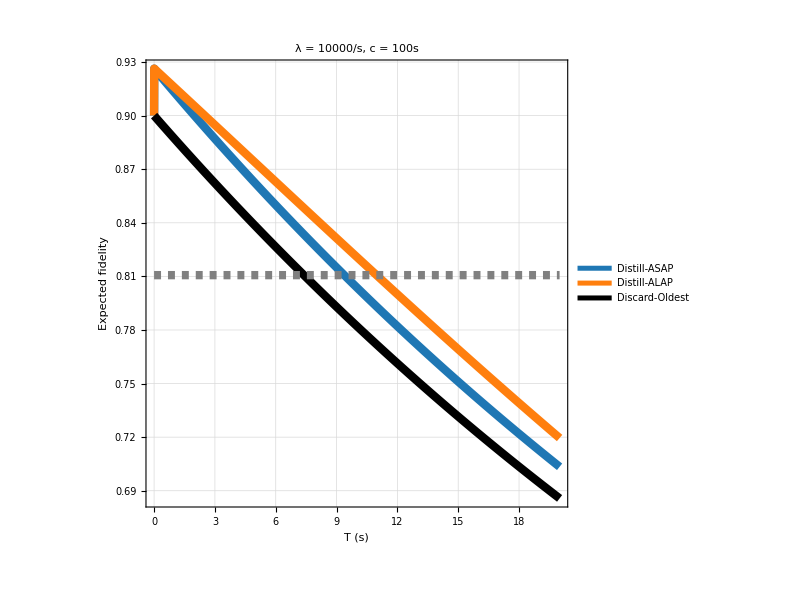

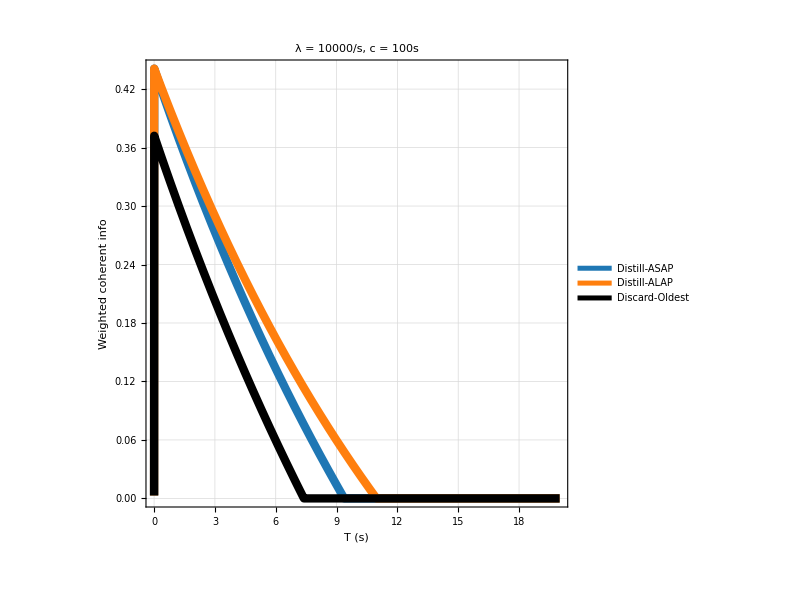

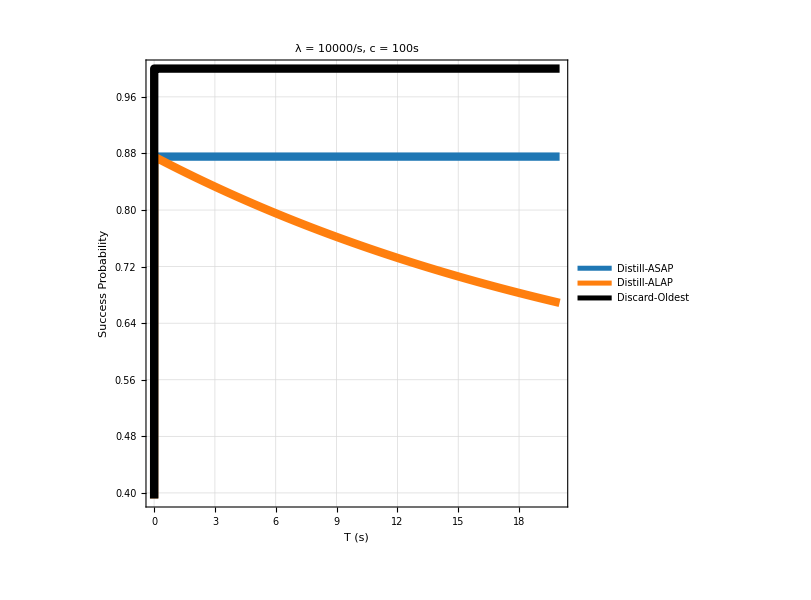

```mathematica
Substitution6= {λ->10000,c->100,F0->0.9};
Plot6 = Plot[
{FDistillASAP/.Substitution6,
FDistillALAP/.Substitution6,
FDiscard/.Substitution6,
0.8107},
{T,0,0.2c /. Substitution6},
PlotStyle->Map[Directive[Thickness[0.01],#]&,{RGBColor["#1f77b4"],RGBColor["#ff7f0e"],Black,Directive[Dashed,Gray]}],
PlotLabel->Style[StringForm["λ = ``/s, c = ``s", λ/.Substitution6,c/.Substitution6], Bold, Black],
PlotLegends->Placed[LineLegend[{"Distill-ASAP","Distill-ALAP","Discard-Oldest"},LegendFunction->(Framed[#,Background->White,FrameStyle->GrayLevel[0.8]]&)],{Right,Top}],
AspectRatio->1,
FrameLabel->{"T (s)","Expected fidelity"}, 
GridLines->Automatic, 
LabelStyle->{FontSize-> FntSize}, 
Frame->True,
ImageSize->600]

PDistillASAPSimplified6 = Simplify[PDistillASAP/.Substitution6];

Plot12 = Plot[
{PDistillASAPSimplified6*CohInfo[FDistillASAP/.Substitution6],
(PDistillALAP/.Substitution6)*CohInfo[FDistillALAP/.Substitution6],
(PDiscard/.Substitution6) *CohInfo[FDiscard/.Substitution6]},
{T,0,0.2c/.Substitution6},
PlotStyle->Map[Directive[Thickness[0.01],#]&,{RGBColor["#1f77b4"],RGBColor["#ff7f0e"],Black,Directive[Dashed,Gray]}],
PlotLabel->Style[StringForm["λ = ``/s, c = ``s", λ/.Substitution6,c/.Substitution6], Bold, Black],
PlotLegends->Placed[LineLegend[{"Distill-ASAP","Distill-ALAP","Discard-Oldest","Positive coh. info. threshold"},LegendFunction->(Framed[#,Background->White,FrameStyle->GrayLevel[0.8]]&)],{Right,Top}],
AspectRatio->1,
FrameLabel->{"T (s)","Weighted coherent info"}, 
GridLines->Automatic, 
LabelStyle->{FontSize-> FntSize}, 
Frame->True,
ImageSize->600]

Plot18 = Plot[
{PDistillASAPSimplified6,
PDistillALAP/.Substitution6,
PDiscard/.Substitution6},
{T,0,0.2c/.Substitution6},
PlotStyle->Map[Directive[Thickness[0.01],#]&,{RGBColor["#1f77b4"],RGBColor["#ff7f0e"],Black,Directive[Dashed,Gray]}],
PlotLabel->Style[StringForm["λ = ``/s, c = ``s", λ/.Substitution6,c/.Substitution6], Bold, Black],
PlotLegends->Placed[LineLegend[{"Distill-ASAP","Distill-ALAP","Discard-Oldest","Positive coh. info. threshold"},LegendFunction->(Framed[#,Background->White,FrameStyle->GrayLevel[0.8]]&)],{Left,Bottom}],
AspectRatio->1,
FrameLabel->{"T (s)","Success Probability"}, 
GridLines->Automatic, 
LabelStyle->{FontSize-> FntSize}, 
Frame->True,
ImageSize->600]
```

### Combining plots

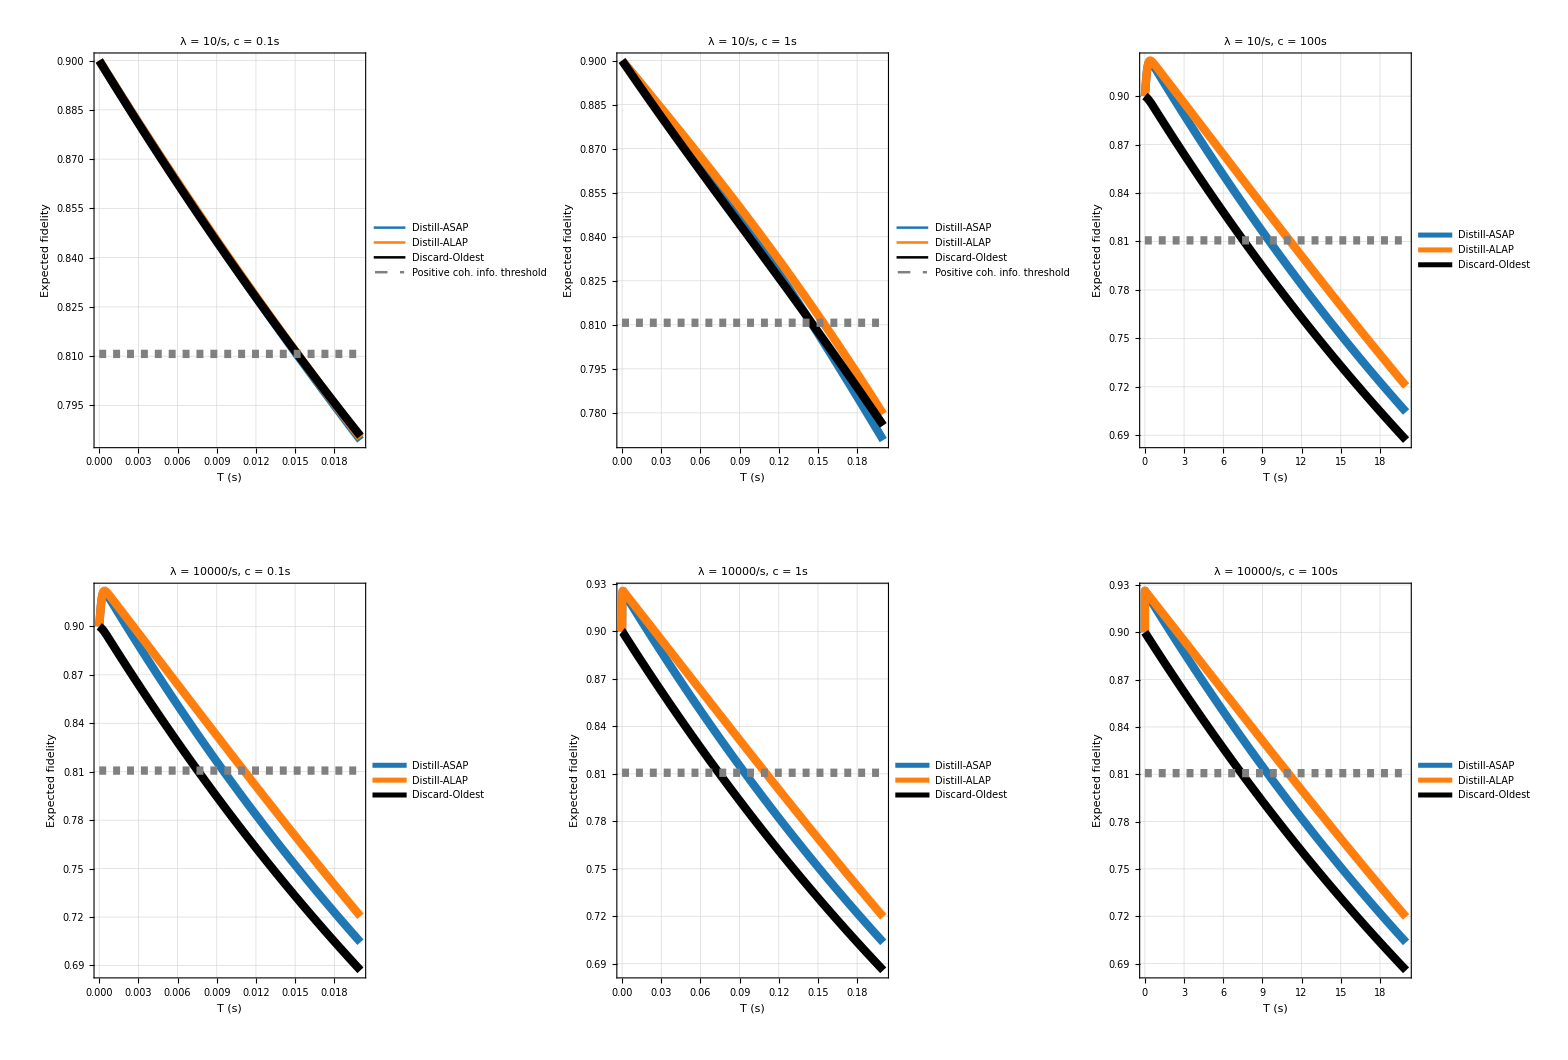

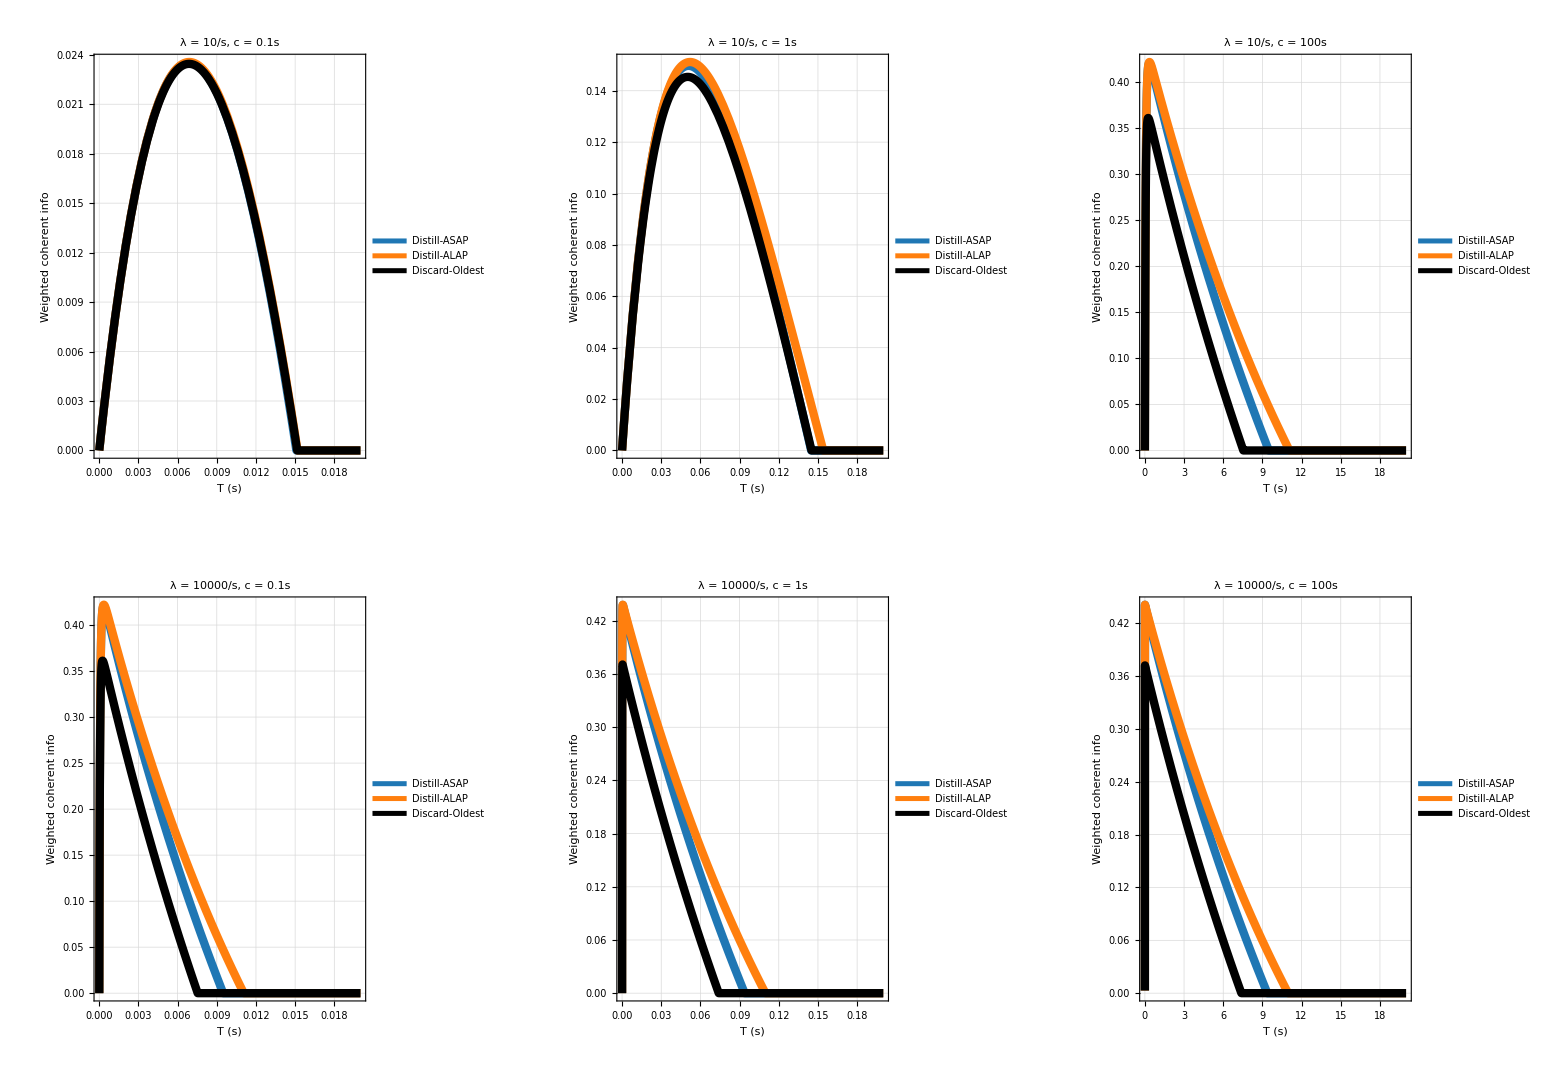

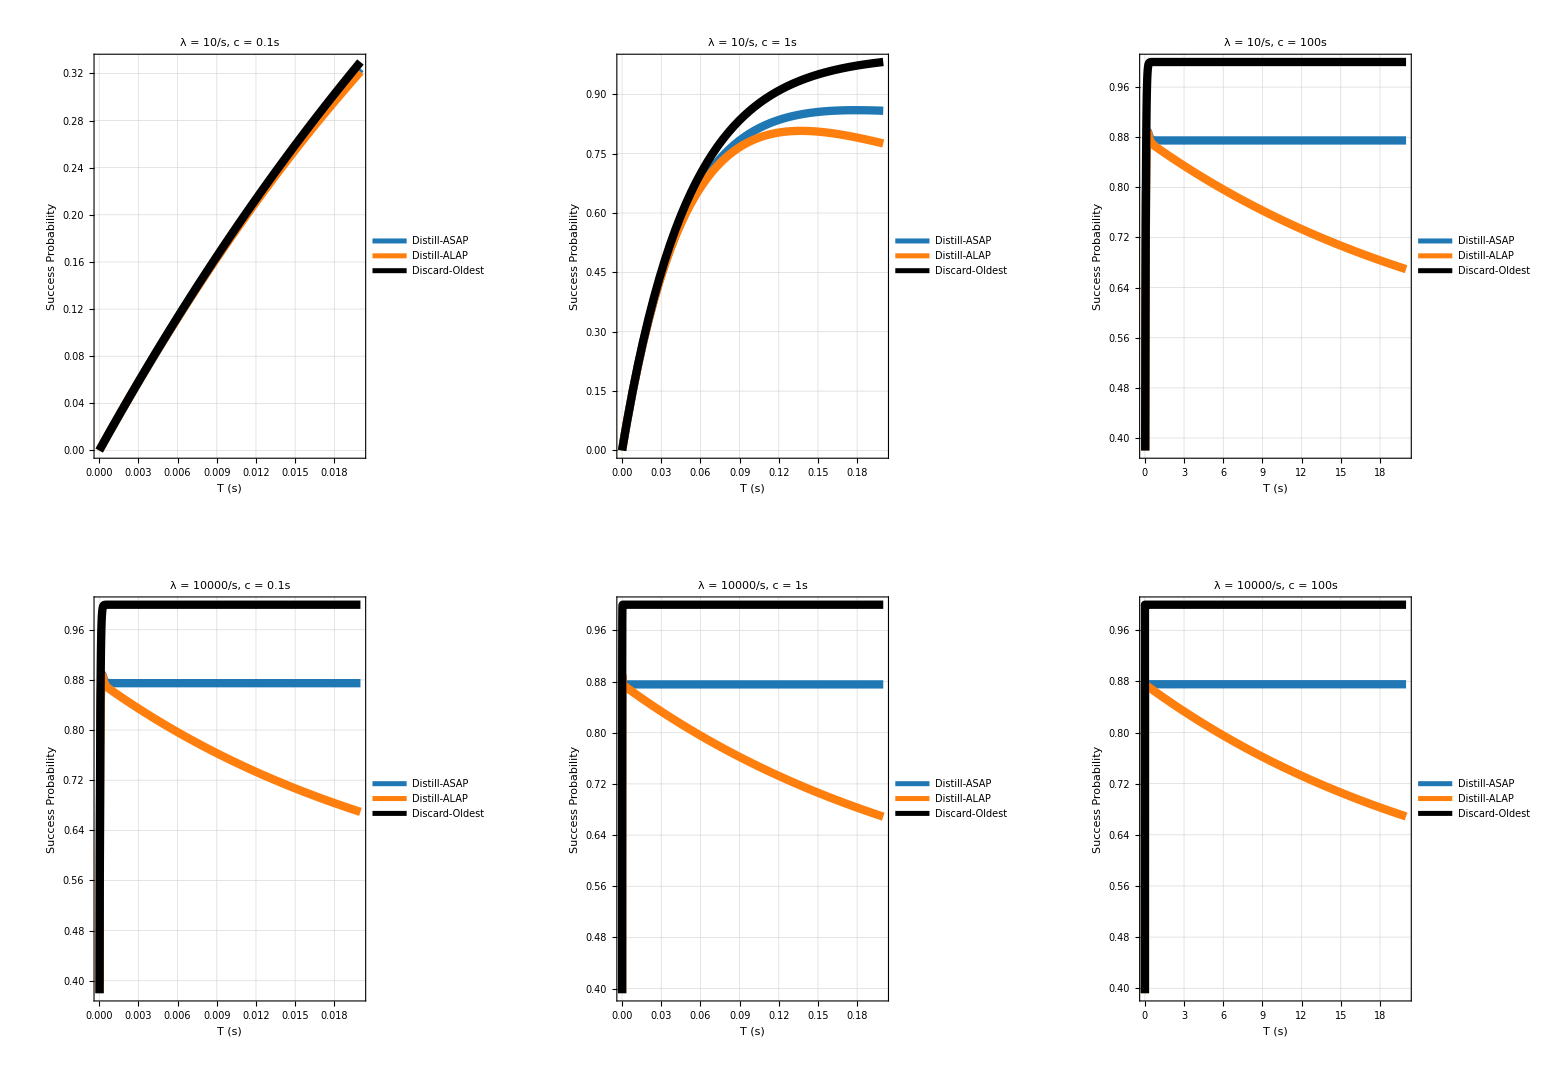

```mathematica
FidPlots = GraphicsGrid[Partition[{Plot1,Plot2,Plot3,Plot4,Plot5,Plot6},3],Spacings->{0.5,0.5},ImageSize->1800]
IcPlots = GraphicsGrid[Partition[{Plot7,Plot8,Plot9,Plot10,Plot11,Plot12},3],Spacings->{0.5,0.5},ImageSize->1800]
PsuccPlots = GraphicsGrid[Partition[{Plot13,Plot14,Plot15,Plot16,Plot17,Plot18},3],Spacings->{0.5,0.5},ImageSize->1800]
```